```mathematica
ClearAll;
```

```mathematica
Clear[P];
P={{7/(√51),-√(2/51),-√(2/51)},{1/(√51),7/(√102),7/(√102)},{1/(√51),7/(√102),7/(√102)}};
```

```mathematica
Needs["Notation`"];
Quiet[
Symbolize[
Subscript[A,1],Subscript[A,2],Subscript[A,3],Subscript[a,1],Subscript[a,2],Subscript[a,3],Subscript[B,1],Subscript[B,2],Subscript[B,3],Subscript[b,1],Subscript[b,2],Subscript[b,3],
Subscript[vtemp,X]
];
];
```

```mathematica
Clear[W,K,v,V,t,x,T,X];
Clear[w0,A,a,B,b,Λ];
Clear[Kmat,Kinv];

Clear[zero];
zero[x_]=0;

W=w0-Sum[Subscript[A,r]Exp[-Subscript[a,r]*T],{r,1,3}]-Sum[Subscript[B,r]Exp[-Subscript[b,r]*T],{r,1,3}]X;
W̄=W/.{T->T̄,X->X̄};
K=-3Log[T+T̄]+X*X̄-(X*X̄)^2/Λ^2;

Subscript[W, T]=D[W,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, X]=D[W,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, TT]=D[W,{T,2}]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, T]=D[K,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X]=D[K,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄]=D[K,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄]=D[K,X̄]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, TT]=D[K,{T,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄ T̄]=D[K,{T̄,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, XX]=D[K,{X,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄ X̄]=D[K,{X̄,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T T̄]=D[K,T,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, TX]=D[K,T,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T X̄]=D[K,T,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X T̄]=D[K,T̄,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄ X̄]=D[K,T̄,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X X̄]=D[K,X,X̄]/.{OverBar'->zero,OverBar''->zero};

DTW=Subscript[W, T]+Subscript[K, T]*W;
OverBar[DTW]=DTW/.{T->T̄,T̄->T,X->X̄,X̄->X};
DXW=Subscript[W, X]+Subscript[K, X]*W;
OverBar[DXW]=DXW/.{T->T̄,T̄->T,X->X̄,X̄->X};

Kmat={{Subscript[K, T T̄],Subscript[K, T X̄]},{Subscript[K, X T̄],Subscript[K, X X̄]}};
Kinv=Inverse[Kmat];
Subscript[invK, T T̄]=Kinv[[1,1]];
Subscript[invK, T X̄]=Kinv[[1,2]];
Subscript[invK, X T̄]=Kinv[[2,1]];
Subscript[invK, X X̄]=Kinv[[2,2]];

vtemp=Exp[K]*(Subscript[invK, T T̄]*(DTW)*(OverBar[DTW])+Subscript[invK, T X̄]*(DTW)*(OverBar[DXW])+Subscript[invK, X T̄]*(DXW)*(OverBar[DTW])+Subscript[invK, X X̄]*(DXW)*(OverBar[DXW])-3W*W̄);
vxtemp=D[vtemp,X]/.{OverBar'->zero,OverBar''->zero};
vttemp=D[vtemp,T]/.{OverBar'->zero,OverBar''->zero};
```

```mathematica
Print["W=",W];
Print["K=",K];

Print["W_T=",Subscript[W, T]];
Print["W_X=",Subscript[W, X]];
Print["K_T=",Subscript[K, T]];
Print["K_X=",Subscript[K, X]];
Print["K_(T̄)=",Subscript[K, T̄]];
Print["K_(X̄)=",Subscript[K, X̄]];

Print["K_TT=",Subscript[K, TT]];
Print["K_(T̄)=",Subscript[K, T̄ T̄]];
Print["K_XX=",Subscript[K, XX]];
Print["K_(X̄)=",Subscript[K, X̄ X̄]];
Print["K_(T OverscriptBox[T, _])=",Subscript[K, T T̄]];
Print["K_TX=",Subscript[K, TX]];
Print["K_(T OverscriptBox[X, _])=",Subscript[K, T X̄]];
Print["K_(X OverscriptBox[T, _])=",Subscript[K, X T̄]];
Print["K_(T̄)=",Subscript[K, T̄ X̄]];
Print["K_(X OverscriptBox[X, _])=",Subscript[K, X X̄]];

Print["K_(I OverscriptBox[J, _])=",Kmat//MatrixForm];
Print["K^(I OverscriptBox[J, _])=",Kinv//MatrixForm];

Print["D_TW=",DTW];
Print["D_(T̄)W̄=",OverBar[DTW]];
Print["D_XW=",DXW];
Print["D_(X̄)W̄=",OverBar[DXW]];

Print["V=",vtemp];
Print["V_X=",vxtemp];
```

Polonyiモデル

```mathematica
Clear[W,K,v,V,t,x,T,X];
Clear[w0,A,a,B,b,Λ];
Clear[Kmat,Kinv];

Clear[zero];
zero[x_]=0;

W=w0-B X;
W̄=W/.{T->T̄,X->X̄};
K=X*X̄;

Subscript[W, T]=D[W,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, X]=D[W,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, TT]=D[W,{T,2}]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, T]=D[K,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X]=D[K,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄]=D[K,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄]=D[K,X̄]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, TT]=D[K,{T,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄ T̄]=D[K,{T̄,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, XX]=D[K,{X,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄ X̄]=D[K,{X̄,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T T̄]=D[K,T,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, TX]=D[K,T,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T X̄]=D[K,T,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X T̄]=D[K,T̄,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄ X̄]=D[K,T̄,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X X̄]=D[K,X,X̄]/.{OverBar'->zero,OverBar''->zero};

DTW=Subscript[W, T]+Subscript[K, T]*W;
OverBar[DTW]=DTW/.{T->T̄,T̄->T,X->X̄,X̄->X};
DXW=Subscript[W, X]+Subscript[K, X]*W;
OverBar[DXW]=DXW/.{T->T̄,T̄->T,X->X̄,X̄->X};

(*Kmat={{Subscript[K, T T̄],Subscript[K, T X̄]},{Subscript[K, X T̄],Subscript[K, X X̄]}};
Kinv=Inverse[Kmat];*)

Subscript[invK, T T̄]=0;
Subscript[invK, T X̄]=0;
Subscript[invK, X T̄]=0;
Subscript[invK, X X̄]=1/Subscript[K, X X̄];

vtemp=Exp[K]*(Subscript[invK, T T̄]*(DTW)*(OverBar[DTW])+Subscript[invK, T X̄]*(DTW)*(OverBar[DXW])+Subscript[invK, X T̄]*(DXW)*(OverBar[DTW])+Subscript[invK, X X̄]*(DXW)*(OverBar[DXW])-3W*W̄);
vxtemp=D[vtemp,X]/.{OverBar'->zero,OverBar''->zero};
vttemp=D[vtemp,T]/.{OverBar'->zero,OverBar''->zero};

Print[vtemp]
```

ⅇ^(X X̄) (-3 (w0-B X) (w0-B X̄)+(-B+(w0-B X) X̄) (-B+X (w0-B X̄)))

```mathematica
Λ=Infinity;
v=vtemp/.{X->ReX,X̄->ReX};
V=FullSimplify[ComplexExpand[v/.{X->ReX,X̄->ReX}]]/.w0->-B(2-Sqrt[3]);
vxtemppolonyi=D[V,ReX];
Solve[V==0,ReX,Reals][[1]]
```

{ReX→-1+√3}

```mathematica
N[Exp[-4Pi^2]]
```

7.15717×10^-18

KKLTモデル

```mathematica
Clear[W,K,v,V,t,x,T,X];
Clear[w0,A,a,B,b,Λ];
Clear[Kmat,Kinv];

Clear[zero];
zero[x_]=0;

W=w0-A Exp[-a T];
W̄=W/.{T->T̄};
K=-3Log[T+T̄];

Subscript[W, T]=D[W,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, X]=D[W,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, TT]=D[W,{T,2}]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, T]=D[K,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X]=D[K,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄]=D[K,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄]=D[K,X̄]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, TT]=D[K,{T,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄ T̄]=D[K,{T̄,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, XX]=D[K,{X,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄ X̄]=D[K,{X̄,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T T̄]=D[K,T,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, TX]=D[K,T,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T X̄]=D[K,T,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X T̄]=D[K,T̄,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄ X̄]=D[K,T̄,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X X̄]=D[K,X,X̄]/.{OverBar'->zero,OverBar''->zero};

DTW=Subscript[W, T]+Subscript[K, T]*W;
OverBar[DTW]=DTW/.{T->T̄,T̄->T,X->X̄,X̄->X};
DXW=Subscript[W, X]+Subscript[K, X]*W;
OverBar[DXW]=DXW/.{T->T̄,T̄->T,X->X̄,X̄->X};

(*
Kmat={{Subscript[K, T T̄],Subscript[K, T X̄]},{Subscript[K, X T̄],Subscript[K, X X̄]}};
Kinv=Inverse[Kmat];
*)

Subscript[invK, T T̄]=1/Subscript[K, T T̄];
Subscript[invK, T X̄]=0;
Subscript[invK, X T̄]=0;
Subscript[invK, X X̄]=0;

vtemp=Exp[K]*(Subscript[invK, T T̄]*(DTW)*(OverBar[DTW])+Subscript[invK, T X̄]*(DTW)*(OverBar[DXW])+Subscript[invK, X T̄]*(DXW)*(OverBar[DTW])+Subscript[invK, X X̄]*(DXW)*(OverBar[DXW])-3W*W̄);
vxtemp=D[vtemp,X]/.{OverBar'->zero,OverBar''->zero};
vttemp=D[vtemp,T]/.{OverBar'->zero,OverBar''->zero};
```

```mathematica
tmin=1.2558664;tmax=1.2558666;

valB=10^(-16);valw0=10^(-20);
valA=1;vala=4Pi^2;
V=FullSimplify[ComplexExpand[vtemp/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]];
veqn=V/.{A->valA,a->vala,B->valB,w0->valw0};
vteqn=FullSimplify@ComplexExpand[D[veqn,ReT]]/.{A->valA,a->vala,B->valB,w0->valw0};

solvt=FindInstance[vteqn==0,{ReT},Reals,WorkingPrecision->1000][[1]];

ret=N[ReT/.solvt];
Print[ret];
Print["V|_0=",N[veqn/.{ReT->ret}]];

(*Print[Plot[vteqn/.{ReT->t,ReX->rex},{t,tmin,tmax},WorkingPrecision->10000]];
Print[Plot[veqn/.{ReT->t,ReX->rex},{t,tmin,tmax},WorkingPrecision->10000]];*)
```

1.25587

V|_0=-1.78366×10^-41

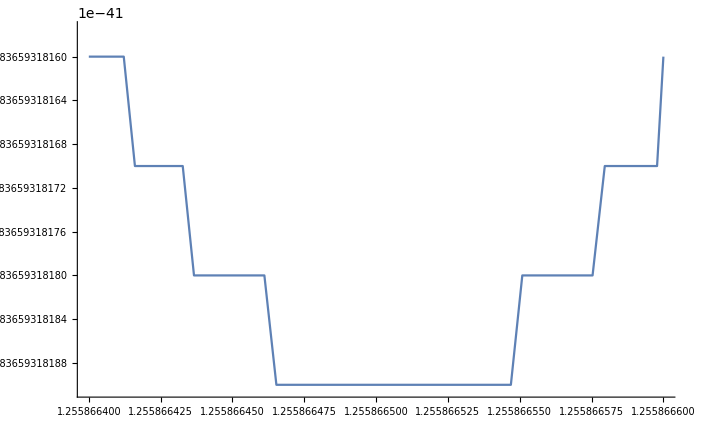
ReT=1.25587
"V|_0="-1.78366×10^-41
-Graphics-

Polonyi-KKLTモデル

```mathematica
Clear[W,K,v,V,t,x,T,X];
Clear[w0,A,a,B,b,Λ];
Clear[Kmat,Kinv];

Clear[zero];
zero[x_]=0;

W=w0-A Exp[-a T]+B X;
W̄=W/.{T->T̄,X->X̄};
K=-3Log[T+T̄]+X*X̄;

Subscript[W, T]=D[W,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, X]=D[W,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, TT]=D[W,{T,2}]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, T]=D[K,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X]=D[K,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄]=D[K,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄]=D[K,X̄]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, TT]=D[K,{T,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄ T̄]=D[K,{T̄,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, XX]=D[K,{X,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄ X̄]=D[K,{X̄,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T T̄]=D[K,T,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, TX]=D[K,T,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T X̄]=D[K,T,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X T̄]=D[K,T̄,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄ X̄]=D[K,T̄,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X X̄]=D[K,X,X̄]/.{OverBar'->zero,OverBar''->zero};

DTW=Subscript[W, T]+Subscript[K, T]*W;
OverBar[DTW]=DTW/.{T->T̄,T̄->T,X->X̄,X̄->X};
DXW=Subscript[W, X]+Subscript[K, X]*W;
OverBar[DXW]=DXW/.{T->T̄,T̄->T,X->X̄,X̄->X};

Kmat={{Subscript[K, T T̄],Subscript[K, T X̄]},{Subscript[K, X T̄],Subscript[K, X X̄]}};
Kinv=Inverse[Kmat];
Subscript[invK, T T̄]=Kinv[[1,1]];
Subscript[invK, T X̄]=Kinv[[1,2]];
Subscript[invK, X T̄]=Kinv[[2,1]];
Subscript[invK, X X̄]=Kinv[[2,2]];

vtemp=Exp[K]*(Subscript[invK, T T̄]*(DTW)*(OverBar[DTW])+Subscript[invK, T X̄]*(DTW)*(OverBar[DXW])+Subscript[invK, X T̄]*(DXW)*(OverBar[DTW])+Subscript[invK, X X̄]*(DXW)*(OverBar[DXW])-3W*W̄);
vxtemp=D[vtemp,X]/.{OverBar'->zero,OverBar''->zero};
vttemp=D[vtemp,T]/.{OverBar'->zero,OverBar''->zero};
```

```mathematica
Clear[valA,vala,valB,valb,valw0,Λ];
Λ=Infinity;
V=FullSimplify[ComplexExpand[vtemp/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]];
Blist={10^(-15),10^(-16),10^(-17),10^(-18),10^(-19),10^(-20)};
w0list={10^(-10),10^(-15),10^(-20),10^(-25)};

Do[
valA=1;vala=4Pi^2;valB=Blist[[i]];valw0=w0list[[j]];
Print["------------------------------"];
Print["B=10^",Log10[valB],", w0=10^",Log10[valw0]];
V=FullSimplify[ComplexExpand[vtemp/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]];
veqn=V/.{A->valA,a->vala,B->valB,w0->valw0};
vxeqn=FullSimplify@ComplexExpand[vxtemp/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]/.{A->valA,a->vala,B->valB,w0->valw0};
vteqn=FullSimplify@ComplexExpand[D[veqn,ReT]]/.{A->valA,a->vala,B->valB,w0->valw0};
dtweqn=FullSimplify@ComplexExpand[DTW/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]/.{A->valA,a->vala,B->valB,w0->valw0};
solvt={ReT->0};testt=0;cnt=0;
While[(testt>2||testt<=0)&&cnt<5,
cnt=cnt+1;
TimeConstrained[
solvt=FindInstance[vteqn==0,{ReT,ReX},Reals,RandomSeeding->Automatic,WorkingPrecision->1000][[1]];
,3];
testt=ReT/.solvt;
];
If[cnt==5,Print["===============over==============="];,
valrex=N[ReX/.solvt];valret=N[ReT/.solvt];
Print["(t,x)=",{valret,valrex}];
Print["V|_0=",N[veqn/.solvt],", V_X|_0=",N[vxeqn/.solvt],", V_T|_0=",N[vteqn/.solvt],", D_TW|_0=",N[dtweqn/.solvt]];
];
,{i,1,Length[Blist]},{j,1,Length[w0list]}];
```

------------------------------

B=10^-15, w0=10^-10

(t,x)={0.799304,0.528175}

V|_0=8.21764×10^-22, V_X|_0=2.14228×10^-21, V_T|_0=0., D_TW|_0=-1.86847×10^-10

------------------------------

B=10^-15, w0=10^-15

$Aborted

A=1, a=4 π^2
"------------------------------"
"B=10^"-16", w0=10^"-20
"(t,x)="{1.03706,-0.501318}
"V|_0="1.21493×10^-33", V_X|_0="-4.20142×10^-34", V_T|_0="0.", D_TW|_0="-4.70379×10^-18

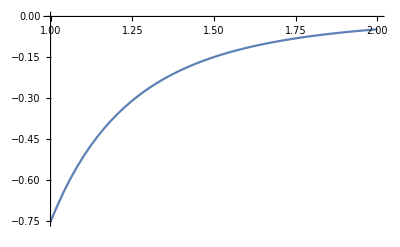

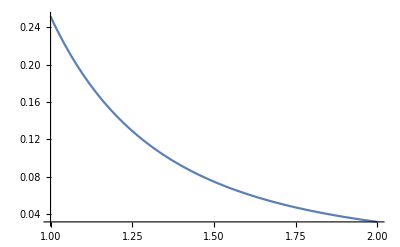

```mathematica
tmin=1.0;tmax=2.0;

valB=-1;valw0=2.165851009527*10^(-18);
valA=1;vala=4Pi^2;
V=FullSimplify[ComplexExpand[vtemp/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]];
veqn=V/.{A->valA,a->vala,B->valB,w0->valw0};
vteqn=FullSimplify@ComplexExpand[D[veqn,ReT]]/.{A->valA,a->vala,B->valB,w0->valw0};

ret=1.0370575693100967;
rex=0.5013180379857513;

Print[Plot[vteqn/.{ReT->t,ReX->rex},{t,tmin,tmax},WorkingPrecision->10000]];
Print[Plot[veqn/.{ReT->t,ReX->rex},{t,tmin,tmax},WorkingPrecision->10000]];
```

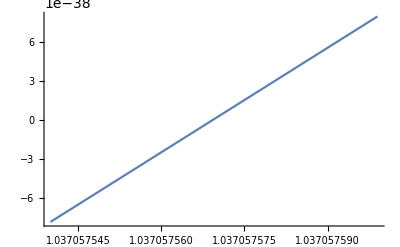
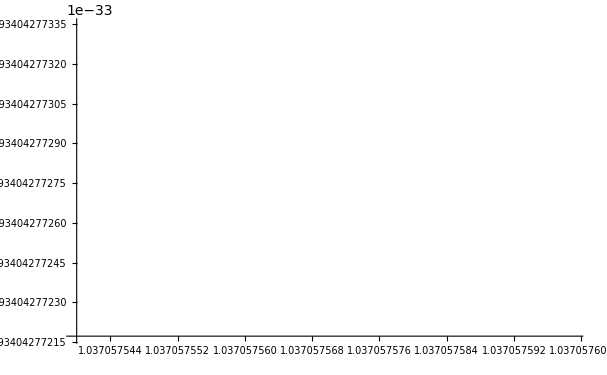
A=1, a=4 π^2
"------------------------------"
"B=10^"-16", w0=10^"-20
"(t,x)="{1.03706,-0.501318}
"V|_0="1.21493×10^-33", V_X|_0="-4.20142×10^-34", V_T|_0="0.", D_TW|_0="-4.70379×10^-18

tmin=1.03705754;tmax=1.037057599;

valB=10^(-16);valw0=10^(-20);
valA=1;vala=4Pi^2;
V=FullSimplify[ComplexExpand[vtemp/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]];
veqn=V/.{A->valA,a->vala,B->valB,w0->valw0};
vteqn=FullSimplify@ComplexExpand[D[veqn,ReT]]/.{A->valA,a->vala,B->valB,w0->valw0};

ret=1.0370575693100967;
rex=-0.5013180379857513;

Print[Plot[vteqn/.{ReT->t,ReX->rex},{t,tmin,tmax},WorkingPrecision→10000]];
Print[Plot[veqn/.{ReT->t,ReX->rex},{t,tmin,tmax},WorkingPrecision→10000]];
-Graphics-
-Graphics-

今回のモデル

```mathematica
Clear[W,K,v,V,t,x,T,X];
Clear[w0,A,a,B,b,Λ];
Clear[Kmat,Kinv];

Clear[zero];
zero[x_]=0;

W=w0-A Exp[-a T]-B Exp[-b T] X;
W̄=W/.{T->T̄,X->X̄};
K=-3Log[T+T̄]+X*X̄;

Subscript[W, T]=D[W,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, X]=D[W,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, TT]=D[W,{T,2}]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, T]=D[K,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X]=D[K,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄]=D[K,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄]=D[K,X̄]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, TT]=D[K,{T,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄ T̄]=D[K,{T̄,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, XX]=D[K,{X,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄ X̄]=D[K,{X̄,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T T̄]=D[K,T,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, TX]=D[K,T,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T X̄]=D[K,T,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X T̄]=D[K,T̄,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄ X̄]=D[K,T̄,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X X̄]=D[K,X,X̄]/.{OverBar'->zero,OverBar''->zero};

DTW=Subscript[W, T]+Subscript[K, T]*W;
OverBar[DTW]=DTW/.{T->T̄,T̄->T,X->X̄,X̄->X};
DXW=Subscript[W, X]+Subscript[K, X]*W;
OverBar[DXW]=DXW/.{T->T̄,T̄->T,X->X̄,X̄->X};

Kmat={{Subscript[K, T T̄],Subscript[K, T X̄]},{Subscript[K, X T̄],Subscript[K, X X̄]}};
Kinv=Inverse[Kmat];
Subscript[invK, T T̄]=Kinv[[1,1]];
Subscript[invK, T X̄]=Kinv[[1,2]];
Subscript[invK, X T̄]=Kinv[[2,1]];
Subscript[invK, X X̄]=Kinv[[2,2]];

vtemp=Exp[K]*(Subscript[invK, T T̄]*(DTW)*(OverBar[DTW])+Subscript[invK, T X̄]*(DTW)*(OverBar[DXW])+Subscript[invK, X T̄]*(DXW)*(OverBar[DTW])+Subscript[invK, X X̄]*(DXW)*(OverBar[DXW])-3W*W̄);
vxtemp=D[vtemp,X]/.{OverBar'->zero,OverBar''->zero};
vttemp=D[vtemp,T]/.{OverBar'->zero,OverBar''->zero};
```

```mathematica
Clear[valA,vala,valB,valb,valw0,Λ];
V=FullSimplify[ComplexExpand[vtemp/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]];
Blist={10,5,2,1,0.5,0.1,0.01,10^(-3),10^(-5),10^(-7)};
blist={4Pi^2-10(*,4Pi^2-5,4Pi^2-1,4Pi^2,4Pi^2+1,4Pi^2+5,4Pi^2+10*)};
alist={(*4Pi^2-10,4Pi^2-5,4Pi^2-1,4Pi^2,4Pi^2+1,4Pi^2+5,*)4Pi^2+10};
w0list={10^(-20)};

Do[
valA=1;vala=alist[[l]];valb=blist[[k]];valB=Blist[[i]];valw0=w0list[[j]];
Print["------------------------------"];
Print["B=",valB,", w0=10^",Log10[valw0],", a=",vala,", b=",valb];
V=FullSimplify[ComplexExpand[vtemp/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]];
veqn=V/.{A->valA,a->vala,B->valB,w0->valw0,b->valb};
vxeqn=FullSimplify@ComplexExpand[vxtemp/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]/.{A->valA,a->vala,B->valB,w0->valw0,b->valb};
vteqn=FullSimplify@ComplexExpand[D[veqn,ReT]]/.{A->valA,a->vala,B->valB,w0->valw0,b->valb};
dtweqn=FullSimplify@ComplexExpand[DTW/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]/.{A->valA,a->vala,B->valB,w0->valw0,b->valb};
solvt={ReT->0};testt=0;cnt=0;
While[(testt>1.5||testt<=0)&&cnt<10,
cnt=cnt+1;
TimeConstrained[
solvt=FindInstance[vteqn==0,{ReT,ReX},Reals,RandomSeeding->Automatic,WorkingPrecision->10000][[1]];
,10];
testt=ReT/.solvt;
];
If[cnt>=10,Print["===============over==============="];,
valrex=N[ReX/.solvt];valret=N[ReT/.solvt];
Print["(t,x)=",{valret,valrex}];
Print["V|_0=",N[veqn/.solvt],", V_X|_0=",N[vxeqn/.solvt],", V_T|_0=",N[vteqn/.solvt],", D_TW|_0=",N[dtweqn/.solvt]];
];
,{i,1,Length[Blist]},{j,1,Length[w0list]},{k,1,Length[blist]},{l,1,Length[alist]}];
```

------------------------------

B=10, w0=10^-20, a=10+4 π^2, b=-10+4 π^2

$Aborted

```mathematica
Clear[valA,vala,valB,valb,valw0,Λ];
V=FullSimplify[ComplexExpand[vtemp/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]];
Blist={5};
blist=Table[4Pi^2+i,{i,-10,10,0.5}];
alist=Table[4Pi^2+i,{i,-10,10,0.5}];
w0list=Table[10^(-20+i),{i,-2,2,0.1}];

Clear[list,cnt];
cnt=0;

Do[
cnt=cnt+1;
valA=1;vala=alist[[l]];valb=blist[[k]];valB=Blist[[i]];valw0=w0list[[j]];
(*
Print["------------------------------"];
Print["B=",valB,", w0=10^",Log10[valw0],", a=",vala,", b=",valb];
*)
V=FullSimplify[ComplexExpand[vtemp/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]];
veqn=V/.{A->valA,a->vala,B->valB,w0->valw0,b->valb};
(*
vxeqn=FullSimplify@ComplexExpand[vxtemp/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]/.{A->valA,a->vala,B->valB,w0->valw0,b->valb};
vteqn=FullSimplify@ComplexExpand[D[veqn,ReT]]/.{A->valA,a->vala,B->valB,w0->valw0,b->valb};
dtweqn=FullSimplify@ComplexExpand[DTW/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]/.{A->valA,a->vala,B->valB,w0->valw0,b->valb};
*)
solfindminimum={ReT->0,ReX->0};
TimeConstraint[
Quiet[
solfindminimum=FindMinimum[veqn/.{ReT->t,ReX->x},{{t,1.0},{x,0.0}},Method->"InteriorPoint",AccuracyGoal->100,PrecisionGoal->100,WorkingPrecision->10000,MaxIterations->500][[2]];

(*
valrex=N[ReX/.{ReT->t,ReX->x}/.solfindminimum];
valret=N[ReT/.{ReT->t,ReX->x}/.solfindminimum];
*)

X=N[veqn/.{ReT->t,ReX->x}/.solfindminimum];
(*
Print["(t,x)=",{valret,valrex}];
Print["V|_0=",X,", V_X|_0=",N[vxeqn/.{ReT->t,ReX->x}/.solfindminimum],", V_T|_0=",N[vteqn/.{ReT->t,ReX->x}/.solfindminimum],", D_TW|_0=",N[dtweqn/.{ReT->t,ReX->x}/.solfindminimum]];
*)
list[cnt,1]=valb;list[cnt,2]=X;
];
,10];
,{i,1,Length[Blist]},{j,1,Length[w0list]},{k,1,Length[blist]},{l,1,Length[alist]}];
plotlist=Table[list[i,j],{i,1,cnt},{j,1,2}];
Print[ListPlot[plotlist]];
```

V|_0=-2.18298×10^-41

<T>=1.19

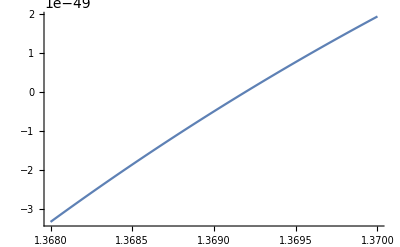

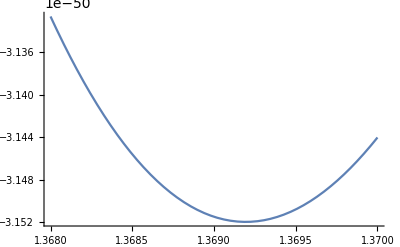

```mathematica
tmin=1.368;tmax=1.370;

valB=2;valw0=10^(-20);
valA=1;vala=10+4 π^2;valb=1+4 π^2;

rex=-1.7637172552280433*10^(-6);

V=FullSimplify[ComplexExpand[vtemp/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]];
veqn=V/.{A->valA,a->vala,B->valB,w0->valw0,b->valb};
vteqn=FullSimplify@ComplexExpand[D[veqn,ReT]]/.{A->valA,a->vala,B->valB,w0->valw0,b->valb};

Quiet[
solfindminimum=FindMinimum[veqn/.{ReT->t,ReX->x},{{t,1.0},{x,0.0}},Method->"InteriorPoint",AccuracyGoal->100,PrecisionGoal->100,WorkingPrecision->10000,MaxIterations->500];
];

Print["V|_0=",solfindminimum[[1]]];
Print["<T>=",N[t/.solfindminimum[[2]],4]];

Print[Plot[vteqn/.{ReT->t,ReX->rex},{t,tmin,tmax},WorkingPrecision->10000]];
Print[Plot[veqn/.{ReT->t,ReX->rex},{t,tmin,tmax},WorkingPrecision->10000]];
```

Reference pointの計算

```mathematica
valw0=10^(-30);valA=3;vala=4Pi^2;valB=0.1;valb=4Pi^2+30;
Subscript[vtemp, X]=D[vtemp,X]/.{OverBar'->zero,OverBar''->zero};
dtw=ComplexExpand[DTW/.{Subscript[A, 1]->A,Subscript[A, 2]->0,Subscript[A, 3]->0,Subscript[a, 1]->a,Subscript[a, 2]->0,Subscript[a, 3]->0,Subscript[B, 1]->B,Subscript[B, 2]->0,Subscript[B, 3]->0,Subscript[b, 1]->b,Subscript[b, 2]->0,Subscript[b, 3]->0,T->ReT+I ImT,T̄->ReT-I ImT,X->ReX+I ImX,X̄->ReX-I ImX,Λ->Infinity}]/.{w0->valw0,A->valA,a->vala,B->valB,b->valb};
dv=vtemp/.{Subscript[A, 1]->A,Subscript[A, 2]->0,Subscript[A, 3]->0,Subscript[a, 1]->a,Subscript[a, 2]->0,Subscript[a, 3]->0,Subscript[B, 1]->B,Subscript[B, 2]->0,Subscript[B, 3]->0,Subscript[b, 1]->b,Subscript[b, 2]->0,Subscript[b, 3]->0,T->ReT+I ImT,T̄->ReT-I ImT,X->ReX+I ImX,X̄->ReX-I ImX,Λ->Infinity}/.{w0->valw0,A->valA,a->vala,B->valB,b->valb};
Subscript[dv, X]=Subscript[vtemp, X]/.{Subscript[A, 1]->A,Subscript[A, 2]->0,Subscript[A, 3]->0,Subscript[a, 1]->a,Subscript[a, 2]->0,Subscript[a, 3]->0,Subscript[B, 1]->B,Subscript[B, 2]->0,Subscript[B, 3]->0,Subscript[b, 1]->b,Subscript[b, 2]->0,Subscript[b, 3]->0,T->ReT+I ImT,T̄->ReT-I ImT,X->ReX+I ImX,X̄->ReX-I ImX,Λ->Infinity}/.{w0->valw0,A->valA,a->vala,B->valB,b->valb};
redtw=(3 w0)/(2 ReT)+a A ⅇ^(-a ReT) Cos[a ImT]+(3 A ⅇ^(-a ReT) Cos[a ImT])/(2 ReT)+b B ⅇ^(-b ReT) ReX Cos[b ImT]+(3 B ⅇ^(-b ReT) ReX Cos[b ImT])/(2 ReT)+b B ⅇ^(-b ReT) ImX Sin[b ImT]+(3 B ⅇ^(-b ReT) ImX Sin[b ImT])/(2 ReT)/.{w0->valw0,A->valA,a->vala,B->valB,b->valb};
imdtw=b B ⅇ^(-b ReT) ImX Cos[b ImT]+(3 B ⅇ^(-b ReT) ImX Cos[b ImT])/(2 ReT)-a A ⅇ^(-a ReT) Sin[a ImT]-(3 A ⅇ^(-a ReT) Sin[a ImT])/(2 ReT)-b B ⅇ^(-b ReT) ReX Sin[b ImT]-(3 B ⅇ^(-b ReT) ReX Sin[b ImT])/(2 ReT)/.{w0->valw0,A->valA,a->vala,B->valB,b->valb};
valdtw=dtw/.{w0->valw0,A->valA,a->vala,B->valB,b->valb};
```

```mathematica
solδTtemp=Indeterminate;
solDTW=
{ReT->1.8768762585684815,ImT->0,ReX->1.1886099682514175,ImX->0};
(*cnt=0;
Quiet[
While[solδTtemp===Indeterminate||OverBar[solδTtemp]===Indeterminate||solδXtemp===Indeterminate||OverBar[solδXtemp]===Indeterminate||Abs[Subscript[dv, X]/.solDTW]>10^(-20)||Abs[dv/.solDTW]>10^(-20),
cnt=cnt+1;
solDTW=FindInstance[redtw==0&&imdtw==0&&1.7<ReT<2.5&&0.8<ReX<1.2,{ReT,ImT,ReX,ImX},Reals,RandomSeeding->Automatic,WorkingPrecision->MachinePrecision][[1]];
solδTtemp=solδT/.solDTW;
OverBar[solδTtemp]=OverBar[solδT]/.solDTW;
solδXtemp=solδX/.solDTW;
OverBar[solδXtemp]=OverBar[solδX]/.solDTW;
];
];
Print["cnt=",cnt];*)
Print["D_TW|_0=",valdtw/.solDTW];
Print["V_X|_0=",Subscript[dv, X]/.solDTW];
Print["V|_0=",dv/.solDTW];
Print["Reference poinT: (T,X)=",N[{ReT+I ImT,ReX+I ImX}/.solDTW]];
Print[solDTW];
```

D_TW|_0=3.17482×10^-46+0. ⅈ

V_X|_0=-5.20707×10^-62

V|_0=-1.18412×10^-61

Reference poinT: (T,X)={1.87688,1.18861}

{ReT→1.87688,ImT→0,ReX→1.18861,ImX→0}

valw0=10^(-30);valA=3;vala=4Pi^2;valB=0.1;valb=4Pi^2+30;
w0->valw0,A->valA,a->vala,B->valB,b->valb
T->ReT+I ImT,T̄->ReT-I ImT,X->ReX+I ImX,X̄->ReX-I ImX

"D_TW|_0="-1.5984×10^-30+1.37122×10^-45 ⅈ
"V_X|_0="1.90931×10^-39+1.10452×10^-38 ⅈ
"V|_0="1.57875×10^-39+0. ⅈ
"Reference poinT: (T,X)="{1.87688+1.19366 ⅈ,1.18861-6.87605 ⅈ}
{ReT→1.87688,ImT→1.19366,ReX→1.18861,ImX→-6.87605}

変分の計算

```mathematica
Clear[δT,δX,Vr];

zero[x_]=0;

Vtrue=Vr+Subscript[Vr, T] δT+Subscript[Vr, T̄] OverBar[δT]+Subscript[Vr, X] δX+Subscript[Vr, X̄] OverBar[δX]+(Subscript[Vr, TT] δT^2+Subscript[Vr, T̄ T̄] OverBar[δT]^2+Subscript[Vr, XX] δX^2+Subscript[Vr, X̄ X̄] OverBar[δX]^2+Subscript[Vr, T T̄] δT OverBar[δT]+Subscript[Vr, TX] δT δX+Subscript[Vr, T X̄] δT OverBar[δX]+Subscript[Vr, T̄ X] OverBar[δT] δX+Subscript[Vr, T̄ X̄] OverBar[δT] OverBar[δX]+Subscript[Vr, X X̄] δX OverBar[δX])/2;

eqn1=D[Vtrue,δT]/.{OverBar'->zero};
eqn2=D[Vtrue,OverBar[δT]]/.{OverBar'->zero};
eqn3=D[Vtrue,δX]/.{OverBar'->zero};
eqn4=D[Vtrue,OverBar[δX]]/.{OverBar'->zero};

solδ=Solve[{eqn1==0,eqn2==0,eqn3==0,eqn4==0},{δT,OverBar[δT],δX,OverBar[δX]}][[1]];

Print["δT=",TeXForm[δT/.solδ[[1]]]];
Print["δT̄=",TeXForm[OverBar[δT]/.solδ[[2]]]];
Print["δX=",TeXForm[δX/.solδ[[3]]]];
Print["δX̄=",TeXForm[OverBar[δX]/.solδ[[4]]]];
```

δT=-\frac{\left(\left(\text{Vr}_{\bar{T}^2} \text{Vr}_{\bar{X}^2}-\frac{1}{4} \text{Vr}_{\bar{T} \bar{X}}^2\right) \left(\text{Vr}_{\text{XX}} \text{Vr}_{\bar{X}^2}-\frac{1}{4} \text{Vr}_{X \bar{X}}^2\right)-\left(\frac{1}{2} \text{Vr}_{\bar{X}^2} \text{Vr}_{X \bar{T}}-\frac{1}{4} \text{Vr}_{X \bar{X}} \text{Vr}_{\bar{T} \bar{X}}\right){}^2\right) \left(\left(\text{Vr}_T \text{Vr}_{\bar{X}^2}-\frac{1}{2} \text{Vr}_{\bar{X}} \text{Vr}_{T \bar{X}}\right) \left(\text{Vr}_{\text{XX}} \text{Vr}_{\bar{X}^2}-\frac{1}{4} \text{Vr}_{X \bar{X}}^2\right)-\left(\text{Vr}_X \text{Vr}_{\bar{X}^2}-\frac{1}{2} \text{Vr}_{\bar{X}} \text{Vr}_{X \bar{X}}\right) \left(\frac{1}{2} \text{Vr}_{\text{TX}} \text{Vr}_{\bar{X}^2}-\frac{1}{4} \text{Vr}_{X \bar{X}} \text{Vr}_{T \bar{X}}\right)\right)-\left(\left(\text{Vr}_{\bar{T}} \text{Vr}_{\bar{X}^2}-\frac{1}{2} \text{Vr}_{\bar{X}} \text{Vr}_{\bar{T} \bar{X}}\right) \left(\text{Vr}_{\text{XX}} \text{Vr}_{\bar{X}^2}-\frac{1}{4} \text{Vr}_{X \bar{X}}^2\right)-\left(\text{Vr}_X \text{Vr}_{\bar{X}^2}-\frac{1}{2} \text{Vr}_{\bar{X}} \text{Vr}_{X \bar{X}}\right) \left(\frac{1}{2} \text{Vr}_{\bar{X}^2} \text{Vr}_{X \bar{T}}-\frac{1}{4} \text{Vr}_{X \bar{X}} \text{Vr}_{\bar{T} \bar{X}}\right)\right) \left(\left(\frac{1}{2} \text{Vr}_{T \bar{T}} \text{Vr}_{\bar{X}^2}-\frac{1}{4} \text{Vr}_{T \bar{X}} \text{Vr}_{\bar{T} \bar{X}}\right) \left(\text{Vr}_{\text{XX}} \text{Vr}_{\bar{X}^2}-\frac{1}{4} \text{Vr}_{X \bar{X}}^2\right)-\left(\frac{1}{2} \text{Vr}_{\bar{X}^2} \text{Vr}_{X \bar{T}}-\frac{1}{4} \text{Vr}_{X \bar{X}} \text{Vr}_{\bar{T} \bar{X}}\right) \left(\frac{1}{2} \text{Vr}_{\text{TX}} \text{Vr}_{\bar{X}^2}-\frac{1}{4} \text{Vr}_{X \bar{X}} \text{Vr}_{T \bar{X}}\right)\right)}{\left(\left(\text{Vr}_{\bar{T}^2} \text{Vr}_{\bar{X}^2}-\frac{1}{4} \text{Vr}_{\bar{T} \bar{X}}^2\right) \left(\text{Vr}_{\text{XX}} \text{Vr}_{\bar{X}^2}-\frac{1}{4} \text{Vr}_{X \bar{X}}^2\right)-\left(\frac{1}{2} \text{Vr}_{\bar{X}^2} \text{Vr}_{X \bar{T}}-\frac{1}{4} \text{Vr}_{X \bar{X}} \text{Vr}_{\bar{T} \bar{X}}\right){}^2\right) \left(\left(\text{Vr}_{\text{XX}} \text{Vr}_{\bar{X}^2}-\frac{1}{4} \text{Vr}_{X \bar{X}}^2\right) \left(\text{Vr}_{\text{TT}} \text{Vr}_{\bar{X}^2}-\frac{1}{4} \text{Vr}_{T \bar{X}}^2\right)-\left(\frac{1}{2} \text{Vr}_{\text{TX}} \text{Vr}_{\bar{X}^2}-\frac{1}{4} \text{Vr}_{X \bar{X}} \text{Vr}_{T \bar{X}}\right){}^2\right)-\left(\left(\frac{1}{2} \text{Vr}_{T \bar{T}} \text{Vr}_{\bar{X}^2}-\frac{1}{4} \text{Vr}_{T \bar{X}} \text{Vr}_{\bar{T} \bar{X}}\right) \left(\text{Vr}_{\text{XX}} \text{Vr}_{\bar{X}^2}-\frac{1}{4} \text{Vr}_{X \bar{X}}^2\right)-\left(\frac{1}{2} \text{Vr}_{\bar{X}^2} \text{Vr}_{X \bar{T}}-\frac{1}{4} \text{Vr}_{X \bar{X}} \text{Vr}_{\bar{T} \bar{X}}\right) \left(\frac{1}{2} \text{Vr}_{\text{TX}} \text{Vr}_{\bar{X}^2}-\frac{1}{4} \text{Vr}_{X \bar{X}} \text{Vr}_{T \bar{X}}\right)\right){}^2}

δT̄=\frac{2 \left(\text{Vr}_{\bar{X}} \text{Vr}_{\bar{T} \bar{X}} \text{Vr}_{\text{TX}}^2-2 \text{Vr}_{\bar{T}} \text{Vr}_{\bar{X}^2} \text{Vr}_{\text{TX}}^2-\text{Vr}_{X \bar{T}} \text{Vr}_{\bar{X}} \text{Vr}_{T \bar{X}} \text{Vr}_{\text{TX}}-\text{Vr}_{T \bar{T}} \text{Vr}_{\bar{X}} \text{Vr}_{X \bar{X}} \text{Vr}_{\text{TX}}+2 \text{Vr}_{\bar{T}} \text{Vr}_{T \bar{X}} \text{Vr}_{X \bar{X}} \text{Vr}_{\text{TX}}-\text{Vr}_X \text{Vr}_{T \bar{X}} \text{Vr}_{\bar{T} \bar{X}} \text{Vr}_{\text{TX}}-\text{Vr}_T \text{Vr}_{X \bar{X}} \text{Vr}_{\bar{T} \bar{X}} \text{Vr}_{\text{TX}}+2 \text{Vr}_X \text{Vr}_{T \bar{T}} \text{Vr}_{\bar{X}^2} \text{Vr}_{\text{TX}}+2 \text{Vr}_T \text{Vr}_{X \bar{T}} \text{Vr}_{\bar{X}^2} \text{Vr}_{\text{TX}}-2 \text{Vr}_{\text{XX}} \text{Vr}_{\bar{T}} \text{Vr}_{T \bar{X}}^2+\text{Vr}_X \text{Vr}_{X \bar{T}} \text{Vr}_{T \bar{X}}^2-2 \text{Vr}_{\text{TT}} \text{Vr}_{\bar{T}} \text{Vr}_{X \bar{X}}^2+\text{Vr}_T \text{Vr}_{T \bar{T}} \text{Vr}_{X \bar{X}}^2+2 \text{Vr}_{\text{XX}} \text{Vr}_{T \bar{T}} \text{Vr}_{\bar{X}} \text{Vr}_{T \bar{X}}+2 \text{Vr}_{\text{TT}} \text{Vr}_{X \bar{T}} \text{Vr}_{\bar{X}} \text{Vr}_{X \bar{X}}-\text{Vr}_X \text{Vr}_{T \bar{T}} \text{Vr}_{T \bar{X}} \text{Vr}_{X \bar{X}}-\text{Vr}_T \text{Vr}_{X \bar{T}} \text{Vr}_{T \bar{X}} \text{Vr}_{X \bar{X}}-4 \text{Vr}_{\text{TT}} \text{Vr}_{\text{XX}} \text{Vr}_{\bar{X}} \text{Vr}_{\bar{T} \bar{X}}+2 \text{Vr}_T \text{Vr}_{\text{XX}} \text{Vr}_{T \bar{X}} \text{Vr}_{\bar{T} \bar{X}}+2 \text{Vr}_{\text{TT}} \text{Vr}_X \text{Vr}_{X \bar{X}} \text{Vr}_{\bar{T} \bar{X}}+8 \text{Vr}_{\text{TT}} \text{Vr}_{\text{XX}} \text{Vr}_{\bar{T}} \text{Vr}_{\bar{X}^2}-4 \text{Vr}_T \text{Vr}_{\text{XX}} \text{Vr}_{T \bar{T}} \text{Vr}_{\bar{X}^2}-4 \text{Vr}_{\text{TT}} \text{Vr}_X \text{Vr}_{X \bar{T}} \text{Vr}_{\bar{X}^2}\right)}{-\text{Vr}_{\bar{T} \bar{X}}^2 \text{Vr}_{\text{TX}}^2+4 \text{Vr}_{\bar{T}^2} \text{Vr}_{\bar{X}^2} \text{Vr}_{\text{TX}}^2-4 \text{Vr}_{\bar{T}^2} \text{Vr}_{T \bar{X}} \text{Vr}_{X \bar{X}} \text{Vr}_{\text{TX}}+2 \text{Vr}_{X \bar{T}} \text{Vr}_{T \bar{X}} \text{Vr}_{\bar{T} \bar{X}} \text{Vr}_{\text{TX}}+2 \text{Vr}_{T \bar{T}} \text{Vr}_{X \bar{X}} \text{Vr}_{\bar{T} \bar{X}} \text{Vr}_{\text{TX}}-4 \text{Vr}_{T \bar{T}} \text{Vr}_{X \bar{T}} \text{Vr}_{\bar{X}^2} \text{Vr}_{\text{TX}}-\text{Vr}_{X \bar{T}}^2 \text{Vr}_{T \bar{X}}^2+4 \text{Vr}_{\text{XX}} \text{Vr}_{\bar{T}^2} \text{Vr}_{T \bar{X}}^2-\text{Vr}_{T \bar{T}}^2 \text{Vr}_{X \bar{X}}^2+4 \text{Vr}_{\text{TT}} \text{Vr}_{\bar{T}^2} \text{Vr}_{X \bar{X}}^2+4 \text{Vr}_{\text{TT}} \text{Vr}_{\text{XX}} \text{Vr}_{\bar{T} \bar{X}}^2+2 \text{Vr}_{T \bar{T}} \text{Vr}_{X \bar{T}} \text{Vr}_{T \bar{X}} \text{Vr}_{X \bar{X}}-4 \text{Vr}_{\text{XX}} \text{Vr}_{T \bar{T}} \text{Vr}_{T \bar{X}} \text{Vr}_{\bar{T} \bar{X}}-4 \text{Vr}_{\text{TT}} \text{Vr}_{X \bar{T}} \text{Vr}_{X \bar{X}} \text{Vr}_{\bar{T} \bar{X}}+4 \text{Vr}_{\text{XX}} \text{Vr}_{T \bar{T}}^2 \text{Vr}_{\bar{X}^2}+4 \text{Vr}_{\text{TT}} \text{Vr}_{X \bar{T}}^2 \text{Vr}_{\bar{X}^2}-16 \text{Vr}_{\text{TT}} \text{Vr}_{\text{XX}} \text{Vr}_{\bar{T}^2} \text{Vr}_{\bar{X}^2}}

δX=-\frac{2 \left(-\text{Vr}_{\bar{X}} \text{Vr}_{X \bar{X}} \text{Vr}_{T \bar{T}}^2+2 \text{Vr}_X \text{Vr}_{\bar{X}^2} \text{Vr}_{T \bar{T}}^2+\text{Vr}_{X \bar{T}} \text{Vr}_{\bar{X}} \text{Vr}_{T \bar{X}} \text{Vr}_{T \bar{T}}+\text{Vr}_{\bar{T}} \text{Vr}_{T \bar{X}} \text{Vr}_{X \bar{X}} \text{Vr}_{T \bar{T}}+\text{Vr}_{\text{TX}} \text{Vr}_{\bar{X}} \text{Vr}_{\bar{T} \bar{X}} \text{Vr}_{T \bar{T}}-2 \text{Vr}_X \text{Vr}_{T \bar{X}} \text{Vr}_{\bar{T} \bar{X}} \text{Vr}_{T \bar{T}}+\text{Vr}_T \text{Vr}_{X \bar{X}} \text{Vr}_{\bar{T} \bar{X}} \text{Vr}_{T \bar{T}}-2 \text{Vr}_{\text{TX}} \text{Vr}_{\bar{T}} \text{Vr}_{\bar{X}^2} \text{Vr}_{T \bar{T}}-2 \text{Vr}_T \text{Vr}_{X \bar{T}} \text{Vr}_{\bar{X}^2} \text{Vr}_{T \bar{T}}-\text{Vr}_{\bar{T}} \text{Vr}_{X \bar{T}} \text{Vr}_{T \bar{X}}^2+2 \text{Vr}_X \text{Vr}_{\bar{T}^2} \text{Vr}_{T \bar{X}}^2-\text{Vr}_T \text{Vr}_{\text{TX}} \text{Vr}_{\bar{T} \bar{X}}^2+2 \text{Vr}_{\text{TT}} \text{Vr}_X \text{Vr}_{\bar{T} \bar{X}}^2-2 \text{Vr}_{\text{TX}} \text{Vr}_{\bar{T}^2} \text{Vr}_{\bar{X}} \text{Vr}_{T \bar{X}}+4 \text{Vr}_{\text{TT}} \text{Vr}_{\bar{T}^2} \text{Vr}_{\bar{X}} \text{Vr}_{X \bar{X}}-2 \text{Vr}_T \text{Vr}_{\bar{T}^2} \text{Vr}_{T \bar{X}} \text{Vr}_{X \bar{X}}-2 \text{Vr}_{\text{TT}} \text{Vr}_{X \bar{T}} \text{Vr}_{\bar{X}} \text{Vr}_{\bar{T} \bar{X}}+\text{Vr}_{\text{TX}} \text{Vr}_{\bar{T}} \text{Vr}_{T \bar{X}} \text{Vr}_{\bar{T} \bar{X}}+\text{Vr}_T \text{Vr}_{X \bar{T}} \text{Vr}_{T \bar{X}} \text{Vr}_{\bar{T} \bar{X}}-2 \text{Vr}_{\text{TT}} \text{Vr}_{\bar{T}} \text{Vr}_{X \bar{X}} \text{Vr}_{\bar{T} \bar{X}}+4 \text{Vr}_{\text{TT}} \text{Vr}_{\bar{T}} \text{Vr}_{X \bar{T}} \text{Vr}_{\bar{X}^2}+4 \text{Vr}_T \text{Vr}_{\text{TX}} \text{Vr}_{\bar{T}^2} \text{Vr}_{\bar{X}^2}-8 \text{Vr}_{\text{TT}} \text{Vr}_X \text{Vr}_{\bar{T}^2} \text{Vr}_{\bar{X}^2}\right)}{-\text{Vr}_{\bar{T} \bar{X}}^2 \text{Vr}_{\text{TX}}^2+4 \text{Vr}_{\bar{T}^2} \text{Vr}_{\bar{X}^2} \text{Vr}_{\text{TX}}^2-4 \text{Vr}_{\bar{T}^2} \text{Vr}_{T \bar{X}} \text{Vr}_{X \bar{X}} \text{Vr}_{\text{TX}}+2 \text{Vr}_{X \bar{T}} \text{Vr}_{T \bar{X}} \text{Vr}_{\bar{T} \bar{X}} \text{Vr}_{\text{TX}}+2 \text{Vr}_{T \bar{T}} \text{Vr}_{X \bar{X}} \text{Vr}_{\bar{T} \bar{X}} \text{Vr}_{\text{TX}}-4 \text{Vr}_{T \bar{T}} \text{Vr}_{X \bar{T}} \text{Vr}_{\bar{X}^2} \text{Vr}_{\text{TX}}-\text{Vr}_{X \bar{T}}^2 \text{Vr}_{T \bar{X}}^2+4 \text{Vr}_{\text{XX}} \text{Vr}_{\bar{T}^2} \text{Vr}_{T \bar{X}}^2-\text{Vr}_{T \bar{T}}^2 \text{Vr}_{X \bar{X}}^2+4 \text{Vr}_{\text{TT}} \text{Vr}_{\bar{T}^2} \text{Vr}_{X \bar{X}}^2+4 \text{Vr}_{\text{TT}} \text{Vr}_{\text{XX}} \text{Vr}_{\bar{T} \bar{X}}^2+2 \text{Vr}_{T \bar{T}} \text{Vr}_{X \bar{T}} \text{Vr}_{T \bar{X}} \text{Vr}_{X \bar{X}}-4 \text{Vr}_{\text{XX}} \text{Vr}_{T \bar{T}} \text{Vr}_{T \bar{X}} \text{Vr}_{\bar{T} \bar{X}}-4 \text{Vr}_{\text{TT}} \text{Vr}_{X \bar{T}} \text{Vr}_{X \bar{X}} \text{Vr}_{\bar{T} \bar{X}}+4 \text{Vr}_{\text{XX}} \text{Vr}_{T \bar{T}}^2 \text{Vr}_{\bar{X}^2}+4 \text{Vr}_{\text{TT}} \text{Vr}_{X \bar{T}}^2 \text{Vr}_{\bar{X}^2}-16 \text{Vr}_{\text{TT}} \text{Vr}_{\text{XX}} \text{Vr}_{\bar{T}^2} \text{Vr}_{\bar{X}^2}}

δX̄=-\frac{2 \left(2 \text{Vr}_{\bar{T}^2} \text{Vr}_{\bar{X}} \text{Vr}_{\text{TX}}^2-\text{Vr}_{\bar{T}} \text{Vr}_{\bar{T} \bar{X}} \text{Vr}_{\text{TX}}^2-2 \text{Vr}_{T \bar{T}} \text{Vr}_{X \bar{T}} \text{Vr}_{\bar{X}} \text{Vr}_{\text{TX}}+\text{Vr}_{\bar{T}} \text{Vr}_{X \bar{T}} \text{Vr}_{T \bar{X}} \text{Vr}_{\text{TX}}-2 \text{Vr}_X \text{Vr}_{\bar{T}^2} \text{Vr}_{T \bar{X}} \text{Vr}_{\text{TX}}+\text{Vr}_{\bar{T}} \text{Vr}_{T \bar{T}} \text{Vr}_{X \bar{X}} \text{Vr}_{\text{TX}}-2 \text{Vr}_T \text{Vr}_{\bar{T}^2} \text{Vr}_{X \bar{X}} \text{Vr}_{\text{TX}}+\text{Vr}_X \text{Vr}_{T \bar{T}} \text{Vr}_{\bar{T} \bar{X}} \text{Vr}_{\text{TX}}+\text{Vr}_T \text{Vr}_{X \bar{T}} \text{Vr}_{\bar{T} \bar{X}} \text{Vr}_{\text{TX}}+2 \text{Vr}_{\text{XX}} \text{Vr}_{T \bar{T}}^2 \text{Vr}_{\bar{X}}+2 \text{Vr}_{\text{TT}} \text{Vr}_{X \bar{T}}^2 \text{Vr}_{\bar{X}}-8 \text{Vr}_{\text{TT}} \text{Vr}_{\text{XX}} \text{Vr}_{\bar{T}^2} \text{Vr}_{\bar{X}}-\text{Vr}_T \text{Vr}_{X \bar{T}}^2 \text{Vr}_{T \bar{X}}-2 \text{Vr}_{\text{XX}} \text{Vr}_{\bar{T}} \text{Vr}_{T \bar{T}} \text{Vr}_{T \bar{X}}+\text{Vr}_X \text{Vr}_{T \bar{T}} \text{Vr}_{X \bar{T}} \text{Vr}_{T \bar{X}}+4 \text{Vr}_T \text{Vr}_{\text{XX}} \text{Vr}_{\bar{T}^2} \text{Vr}_{T \bar{X}}-\text{Vr}_X \text{Vr}_{T \bar{T}}^2 \text{Vr}_{X \bar{X}}-2 \text{Vr}_{\text{TT}} \text{Vr}_{\bar{T}} \text{Vr}_{X \bar{T}} \text{Vr}_{X \bar{X}}+\text{Vr}_T \text{Vr}_{T \bar{T}} \text{Vr}_{X \bar{T}} \text{Vr}_{X \bar{X}}+4 \text{Vr}_{\text{TT}} \text{Vr}_X \text{Vr}_{\bar{T}^2} \text{Vr}_{X \bar{X}}+4 \text{Vr}_{\text{TT}} \text{Vr}_{\text{XX}} \text{Vr}_{\bar{T}} \text{Vr}_{\bar{T} \bar{X}}-2 \text{Vr}_T \text{Vr}_{\text{XX}} \text{Vr}_{T \bar{T}} \text{Vr}_{\bar{T} \bar{X}}-2 \text{Vr}_{\text{TT}} \text{Vr}_X \text{Vr}_{X \bar{T}} \text{Vr}_{\bar{T} \bar{X}}\right)}{-\text{Vr}_{\bar{T} \bar{X}}^2 \text{Vr}_{\text{TX}}^2+4 \text{Vr}_{\bar{T}^2} \text{Vr}_{\bar{X}^2} \text{Vr}_{\text{TX}}^2-4 \text{Vr}_{\bar{T}^2} \text{Vr}_{T \bar{X}} \text{Vr}_{X \bar{X}} \text{Vr}_{\text{TX}}+2 \text{Vr}_{X \bar{T}} \text{Vr}_{T \bar{X}} \text{Vr}_{\bar{T} \bar{X}} \text{Vr}_{\text{TX}}+2 \text{Vr}_{T \bar{T}} \text{Vr}_{X \bar{X}} \text{Vr}_{\bar{T} \bar{X}} \text{Vr}_{\text{TX}}-4 \text{Vr}_{T \bar{T}} \text{Vr}_{X \bar{T}} \text{Vr}_{\bar{X}^2} \text{Vr}_{\text{TX}}-\text{Vr}_{X \bar{T}}^2 \text{Vr}_{T \bar{X}}^2+4 \text{Vr}_{\text{XX}} \text{Vr}_{\bar{T}^2} \text{Vr}_{T \bar{X}}^2-\text{Vr}_{T \bar{T}}^2 \text{Vr}_{X \bar{X}}^2+4 \text{Vr}_{\text{TT}} \text{Vr}_{\bar{T}^2} \text{Vr}_{X \bar{X}}^2+4 \text{Vr}_{\text{TT}} \text{Vr}_{\text{XX}} \text{Vr}_{\bar{T} \bar{X}}^2+2 \text{Vr}_{T \bar{T}} \text{Vr}_{X \bar{T}} \text{Vr}_{T \bar{X}} \text{Vr}_{X \bar{X}}-4 \text{Vr}_{\text{XX}} \text{Vr}_{T \bar{T}} \text{Vr}_{T \bar{X}} \text{Vr}_{\bar{T} \bar{X}}-4 \text{Vr}_{\text{TT}} \text{Vr}_{X \bar{T}} \text{Vr}_{X \bar{X}} \text{Vr}_{\bar{T} \bar{X}}+4 \text{Vr}_{\text{XX}} \text{Vr}_{T \bar{T}}^2 \text{Vr}_{\bar{X}^2}+4 \text{Vr}_{\text{TT}} \text{Vr}_{X \bar{T}}^2 \text{Vr}_{\bar{X}^2}-16 \text{Vr}_{\text{TT}} \text{Vr}_{\text{XX}} \text{Vr}_{\bar{T}^2} \text{Vr}_{\bar{X}^2}}

```mathematica
Subscript[Vr, T]=D[v,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[Vr, T̄]=D[v,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[Vr, X]=D[v,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[Vr, X̄]=D[v,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[Vr, TT]=D[v,{T,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[Vr, T̄ T̄]=D[v,{T̄,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[Vr, XX]=D[v,{X,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[Vr, X̄ X̄]=D[v,{X̄,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[Vr, T T̄]=D[v,T,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[Vr, TX]=D[v,T,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[Vr, T X̄]=D[v,T,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[Vr, T̄ X]=D[v,T̄,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[Vr, T̄ X̄]=D[v,T̄,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[Vr, X X̄]=D[v,X,X̄]/.{OverBar'->zero,OverBar''->zero};
```

```mathematica
Clear[solδT,solδX];
valw0=10^(-30);valA=3;vala=4Pi^2;valB=0.1;valb=4Pi^2+30;
{solδT,OverBar[solδT],solδX,OverBar[solδX]}={δT,OverBar[δT],δX,OverBar[δX]}/.solδ;
{solδT,OverBar[solδT],solδX,OverBar[solδX]}={solδT,OverBar[solδT],solδX,OverBar[solδX]}/.{T->ReT+I ImT,T̄->ReT-I ImT,X->ReX+I ImX,X̄->ReX-I ImX};
solδT=solδT/.{w0->valw0,A->valA,a->vala,B->valB,b->valb};
OverBar[solδT]=OverBar[solδT]/.{w0->valw0,A->valA,a->vala,B->valB,b->valb};
solδX=solδX/.{w0->valw0,A->valA,a->vala,B->valB,b->valb};
OverBar[solδX]=OverBar[solδX]/.{w0->valw0,A->valA,a->vala,B->valB,b->valb};
```

```mathematica
solδTtemp=Indeterminate;
cnt=0;
Quiet[
While[solδTtemp===Indeterminate||OverBar[solδTtemp]===Indeterminate||solδXtemp===Indeterminate||OverBar[solδXtemp]===Indeterminate,
cnt=cnt+1;
solDTW=FindInstance[redtw==0&&imdtw==0&&1.7<ReT<2.5&&0.8<ReX<1.2,{ReT,ImT,ReX,ImX},Reals,RandomSeeding->Automatic,WorkingPrecision->MachinePrecision][[1]];
solδTtemp=solδT/.solDTW;
OverBar[solδTtemp]=OverBar[solδT]/.solDTW;
solδXtemp=solδX/.solDTW;
OverBar[solδXtemp]=OverBar[solδX]/.solDTW;
];
];
Print["cnt=",cnt];
Print["Reference point:",{ReT+I ImT,ReX+I ImX}/.solDTW];
```

"D_TW|_0="-1.5984×10^-30+1.37122×10^-45 ⅈ
"V_X|_0="1.90931×10^-39+1.10452×10^-38 ⅈ
"V|_0="1.57875×10^-39+0. ⅈ
"Reference poinT: (T,X)="{1.87688+1.19366 ⅈ,1.18861-6.87605 ⅈ}
{ReT→1.87688,ImT→1.19366,ReX→1.18861,ImX→-6.87605}

```mathematica
Print["δT/t=",Abs[solδTtemp/(ReT+I ImT)]/.solDTW];
Print["δX/x=",Abs[solδXtemp/(ReX+I ImX)]/.solDTW];
```

δT/t=0.0039528

δX/x=0.0127501

結果

"D_TW|_0="-1.5984×10^-30+1.37122×10^-45 ⅈ
"V_X|_0="1.90931×10^-39+1.10452×10^-38 ⅈ
"V|_0="1.57875×10^-39+0. ⅈ
"Reference poinT: (T,X)="{1.87688+1.19366 ⅈ,1.18861-6.87605 ⅈ}
{ReT→1.87688,ImT→1.19366,ReX→1.18861,ImX→-6.87605}

"δT/t="0.0039528
"δX/x="0.0127501

```mathematica
ref=
{ReT->1.8768762585684815,ImT->0,ReX->1.1886099682514175,ImX->0};
Λ=Infinity;
valw0=10^(-30);valA=3;vala=4Pi^2;valB=0.1;valb=4Pi^2+30;

mT=-Exp[K/2]*Subscript[invK, T T̄]*Subscript[W, TT]/.{Subscript[A, 1]->A,Subscript[A, 2]->0,Subscript[A, 3]->0,Subscript[a, 1]->a,Subscript[a, 2]->0,Subscript[a, 3]->0,Subscript[B, 1]->B,Subscript[B, 2]->0,Subscript[B, 3]->0,Subscript[b, 1]->b,Subscript[b, 2]->0,Subscript[b, 3]->0,T->ReT+I ImT,T̄->ReT-I ImT,X->ReX+I ImX,X̄->ReX-I ImX,Λ->Infinity}/.{w0->valw0,A->valA,a->vala,B->valB,b->valb}/.ref;

m32=Exp[K/2]W/.{Subscript[A, 1]->A,Subscript[A, 2]->0,Subscript[A, 3]->0,Subscript[a, 1]->a,Subscript[a, 2]->0,Subscript[a, 3]->0,Subscript[B, 1]->B,Subscript[B, 2]->0,Subscript[B, 3]->0,Subscript[b, 1]->b,Subscript[b, 2]->0,Subscript[b, 3]->0,T->ReT+I ImT,T̄->ReT-I ImT,X->ReX+I ImX,X̄->ReX-I ImX,Λ->Infinity}/.{w0->valw0,A->valA,a->vala,B->valB,b->valb}/.ref;

OverBar[DTW]=DTW/.{T->T̄,T̄->T,X->X̄,X̄->X};
FT=-Exp[K/2]*Subscript[invK, T T̄]*OverBar[DTW]/.{Subscript[A, 1]->A,Subscript[A, 2]->0,Subscript[A, 3]->0,Subscript[a, 1]->a,Subscript[a, 2]->0,Subscript[a, 3]->0,Subscript[B, 1]->B,Subscript[B, 2]->0,Subscript[B, 3]->0,Subscript[b, 1]->b,Subscript[b, 2]->0,Subscript[b, 3]->0,T->ReT+I ImT,T̄->ReT-I ImT,X->ReX+I ImX,X̄->ReX-I ImX,Λ->Infinity}/.{w0->valw0,A->valA,a->vala,B->valB,b->valb}/.ref;

OverBar[DXW]=DXW/.{T->T̄,T̄->T,X->X̄,X̄->X};

FX=-Exp[K/2]*Subscript[invK, X X̄]*OverBar[DXW]/.{Subscript[A, 1]->A,Subscript[A, 2]->0,Subscript[A, 3]->0,Subscript[a, 1]->a,Subscript[a, 2]->0,Subscript[a, 3]->0,Subscript[B, 1]->B,Subscript[B, 2]->0,Subscript[B, 3]->0,Subscript[b, 1]->b,Subscript[b, 2]->0,Subscript[b, 3]->0,T->ReT+I ImT,T̄->ReT-I ImT,X->ReX+I ImX,X̄->ReX-I ImX,Λ->Infinity}/.{w0->valw0,A->valA,a->vala,B->valB,b->valb}/.ref;
vval=vtemp/.{Subscript[A, 1]->A,Subscript[A, 2]->0,Subscript[A, 3]->0,Subscript[a, 1]->a,Subscript[a, 2]->0,Subscript[a, 3]->0,Subscript[B, 1]->B,Subscript[B, 2]->0,Subscript[B, 3]->0,Subscript[b, 1]->b,Subscript[b, 2]->0,Subscript[b, 3]->0,T->ReT+I ImT,T̄->ReT-I ImT,X->ReX+I ImX,X̄->ReX-I ImX,Λ->Infinity}/.{w0->valw0,A->valA,a->vala,B->valB,b->valb}/.ref;
α=(m32*(T+T̄))/(Log[1/m32]*FT)/.{Subscript[A, 1]->A,Subscript[A, 2]->0,Subscript[A, 3]->0,Subscript[a, 1]->a,Subscript[a, 2]->0,Subscript[a, 3]->0,Subscript[B, 1]->B,Subscript[B, 2]->0,Subscript[B, 3]->0,Subscript[b, 1]->b,Subscript[b, 2]->0,Subscript[b, 3]->0,T->ReT+I ImT,T̄->ReT-I ImT,X->ReX+I ImX,X̄->ReX-I ImX,Λ->Infinity}/.{w0->valw0,A->valA,a->vala,B->valB,b->valb}/.ref;

Print["m_T=",mT];
Print["m_(3/2)=",m32];
Print["F^T=",FT];
Print["F^X=",FX];
Print["V=",vval];
Print["α=",α];
```

m_T=4.04769×10^-29

m_(3/2)=2.73138×10^-31

F^T=-5.73161×10^-46

F^X=-3.24654×10^-31

V=-1.18412×10^-61

α=-2.54185×10^13

"m_T="4.04769×10^-29
"m_(3/2)="2.73138×10^-31
"F^T="-5.73161×10^-46
"F^X="-3.24654×10^-31
"V="-1.18412×10^-61
"α="-2.54185×10^13